```mathematica
Clear["`*"]
```

```mathematica
Derived formula from trig. 
Compared to Robert' s spreeuw i have the cos (t) outside the square root
```

cos Derived formula from have i outside root s spreeuw square t the^2 to trig.Compared Robert'

```mathematica
df[t_]=d(1-Cos[t]/(√(n^2-Sin[t]^2)));
```

difference between marginal and paraxial

```mathematica
focalShift=df[t]-df[0];//FullSimplify
```

```mathematica
focalshiftApprox[t_,n_,d_]=Series[focalShift,{t,0,4}]//Normal
```

(d (-1+n^2) t^2)/(2 (n^2)^(3/2))-(d (9-10 n^2+n^4) t^4)/(24 n^4 √(n^2))

variables

```mathematica
ncorr=1.5103;
dcorr=3.5*10^-3;
nquartz=1.453;
dquartz=4*10^-3;
λ=820*10^-9;
```

just the glass plate

```mathematica
pathGlass=focalshiftApprox[t,nquartz,dquartz]
```

0.000724484 t^2+0.000196997 t^4

```mathematica
wavesGlass = (ncorr-1)*pathGlass/λ//Expand
```

450.859 t^2+122.595 t^4

subtract corrected part

```mathematica
difference=pathGlass-focalshiftApprox[t, ncorr,dcorr]
```

0.0000737561 t^2+0.0000372634 t^4

```mathematica
wavesCorrected=(ncorr-1)*difference/λ//Expand
```

45.8997 t^2+23.1896 t^4

Plot 4th order term. Should be ~6 x 0.27 ~1.6 ρ^4 where the 6 comes from the R40 radial zernike term

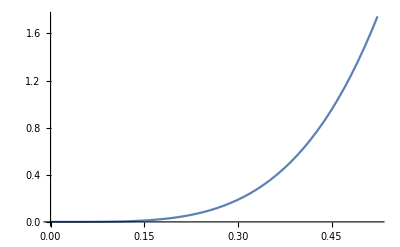

```mathematica
Plot[23.208119707562282* t^4,
{t,0,ArcSin[0.5]}
]
```